## Prepare

```mathematica
imgsize=700;
imgpadding={{70, 20}, {50, 10}};
```

Always use the first element in the vector to be the component of small eigenvalue.

```mathematica
$MachinePrecision
```

15.9546

### Modules

Making Plots

```mathematica
pltNorm[sol_,c1_,c2_,start_,end_]:=Plot[Evaluate[Abs[c1[x]]^2+Abs[c2[x]]^2/.sol[[1]]],{x,start,end},PlotRange->All,ImageSize->imgsize,Frame->True];
```

Plot transitioin Probabilities: Probability of c2

```mathematica
pltProb[sol_,c2_,c1_,start_,end_,pltLabel_,frameLabel_]:=Plot[Evaluate[Abs[c2[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.sol[[1]]],{x,start,end},PlotRange->All,PlotLabel->pltLabel,ImageSize->imgsize,Frame->True,FrameLabel->frameLabel,ImagePadding->imgpadding,PerformanceGoal->"Quality"];
```

Rotation matrices

Rotation from vacuum to instantaneous matter basis

```mathematica
vac2instRotation[a0_,a1_,tv_]:=Module[{thetaxConst,alpha0=a0,alpha1=a1,thetav=tv},thetaxConst=ArcSin[Sin[2thetav]/(√(1+(alpha0+alpha1)^2-2(alpha0+alpha1)Cos[2thetav]))]/2;{{Cos[thetav-thetaxConst],Sin[thetav-thetaxConst]},{-Sin[thetav-thetaxConst],Cos[thetav-thetaxConst]}}]
```

Pauli matrices

```mathematica
sigma3=PauliMatrix[3];
sigma1=PauliMatrix[1];
```

Conversion from length (km) to energy (eV): 197.33 MeV*fm=1 =>

```mathematica
hbarc=197.3269788
```

197.327

```mathematica
km2eV[km_]:=Module[{length=km},(hbarc*10^6)/(km*10^(18))]
eV2km[eV_]:=Module[{energy=eV},(hbarc*10^(-18))/(eV*10^(-6))]
```

### Paramters

Paramters are grabbed from Kneller’s paper

In (averaged) matter basis

```mathematica
N@Pi/4
```

0.785398

```mathematica
θv=0.573(*/180*Pi*)(*Pi/4-0.573/180*Pi*)
energy=20*10^6; (* eV *)
deltam2=3*10^(-3); (* eV^2 *)
(* The following are calculated *)
omegav=deltam2/(2energy); (* 7.5*10^(-11) *) (*eV, delta^2m= 3*10^(-3)eV^2, E =20MeV*)
fraction = 3
α0=Cos[2θv]/fraction;
(* α0=0;*)
(*α1=0;*)
α1=0.1α0;
(*β=0.937*) β=(2Pi*km2eV[5.26])/omegav;
phasem=0;
```

0.573

3

```mathematica
θm=ArcTan[Sin[θv]/(Cos[θv]-α0)]
```

0.657002

Resoance condition for beta is

```mathematica
βr=N[√(1+α0^2-2α0 Cos[2θv])]
```

0.951649

A function that calculates resonance point

```mathematica
resPoint[alpha0_]:=N[√(1+alpha0^2-2alpha0 Cos[2θv])]
```

### Initial Condition

The initial condition in matter basis

```mathematica
initAM={1,0}
```

{1,0}

Rotate to vacuum eigenbasis

```mathematica
vac2instRotation[α0,0,θv]//MatrixForm
initVac=Transpose[vac2instRotation[α0,0,θv]].initAM
```

(0.997826 | -0.0659073
0.0659073 | 0.997826)

{0.997826,-0.0659073}

```mathematica
endpoint=(6*10^9/5)*10^(-5)(* omegav/km2eV[10^4];*)
%//N
```

12000

12000.

```mathematica
N@km2eV[10^(10-2-3)]/omegav
```

0.0000263103

### Test of Defined Functions and Parametser + Check Numbers

```mathematica
"σ3 is "MatrixForm@sigma3
"σ1 is "MatrixForm@sigma1
```

σ3 is  (1 | 0
0 | -1)

σ1 is  (0 | 1
1 | 0)

Test Rotation

```mathematica
vac2instRotationTest=Module[{θv=ArcSin@√0.307},Grid[{{"Zero Matter Potential: "<>ToString@vac2instRotation[0,0,θv]},{"MSW Resonance: "<>ToString@vac2instRotation[Cos[2*θv],0,θv]}}]]
```

Zero Matter Potential: {{1., 0.}, {0., 1.}}
MSW Resonance: {{0.980433, -0.196852}, {0.196852, 0.980433}}

Test Unit convsersion

```mathematica
km2eV[10^(-18)]
eV2km[10^6]
```

1.97327×10^8

1.97327×10^-16

#### Check Numbers

```mathematica
ArcSin[Sin[2θv]/(√(1+(α0+α1)^2-2(α0+α1)Cos[2θv]))]/2
Sin[2ArcTan[Sin[2θv]/(Cos[2θv]-α0)]/2]^2
```

0.645894

0.916643

```mathematica
omegav//N
```

7.5×10^-11

```mathematica
(6/omegav)*10^(-7)*197/Pi//N
```

501656.

```mathematica
1/km2eV[1]//N
```

5.06773×10^9

```mathematica
θv*Pi/180
```

0.0100007

```mathematica
(2Pi/omegav*√(1+α0^2-2α0 Cos[2θv]))*10^(-7)*197
```

1.57059×10^6

```mathematica
(100/omegav)*10^(-7)*197//N
```

2.62667×10^7

## Hamiltonian

### Hamiltonians

The normalized Hamiltonian in vacuum basis is

```mathematica
hamilVacGen[alpha0_,alpha1_,beta_,lambda_,x_]:=Module[{},-1/2 sigma3+lambda/2 Cos[2*θv]sigma3+lambda/2 Sin[2*θv]sigma1]
```

```mathematica
hamilVac[alpha0_,alpha1_,beta_,x_]:=Module[{lambda=alpha0+alpha1*Sin[beta*x+phasem]},-1/2 sigma3+lambda/2 Cos[2*θv]sigma3+lambda/2 Sin[2*θv]sigma1]
```

```mathematica
hamilVac[α0,α1,β,x]
```

{{-0.5+0.206068 (0.137378+0.0137378 Sin[3.14282 x]),0.+0.455561 (0.137378+0.0137378 Sin[3.14282 x])},{0.+0.455561 (0.137378+0.0137378 Sin[3.14282 x]),0.5-0.206068 (0.137378+0.0137378 Sin[3.14282 x])}}

Manually remove sigma3 term

```mathematica
hamilVac1[alpha0_,alpha1_,beta_,x_]:=Module[{lambda=alpha0+alpha1*Sin[beta*x+phasem]},-1/2 sigma3+lambda/2 Sin[2*θv]sigma1]
```

Manually remove sigma1 term

```mathematica
hamilVac3[alpha0_,alpha1_,beta_,x_]:=Module[{lambda=alpha0+alpha1*Sin[beta*x+phasem]},-1/2 sigma3+lambda/2 Cos[2*θv]sigma3]
```

```mathematica
hamilVac2Freq[alpha0_,alpha1_,beta_,x_]:=Module[{lambda=alpha0+alpha1*Sin[beta*x+phasem]+alpha1*Sin[2*beta*x+phasem]},-1/2 sigma3+lambda/2 Cos[2*θv]sigma3+lambda/2 Sin[2*θv]sigma1]
```

```mathematica
hamilVac2FreqClose[alpha0_,alpha1_,beta_,x_]:=Module[{lambda=alpha0+alpha1*Sin[beta*x+phasem]+alpha1*Sin[1.1*beta*x+phasem]},-1/2 sigma3+lambda/2 Cos[2*θv]sigma3+lambda/2 Sin[2*θv]sigma1]
```

```mathematica
hamilVacSquare[alpha0_,alpha1_,beta_,x_]:=Module[{lambda=alpha0+alpha1*UnitStep[Sin[beta*x+phasem]]},-1/2 sigma3+lambda/2 Cos[2*θv]sigma3+lambda/2 Sin[2*θv]sigma1]
```

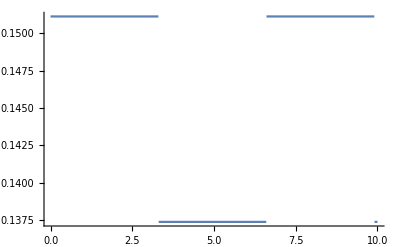

```mathematica
Plot[α0+α1*UnitStep[Sin[βr*x+phasem]],{x,0,10}]
```

## Calculate in Matter Basis

The calculation can be done in averaged matter basis directly.

Hamiltonian in (averaged) Matter basis is

```mathematica
hamilAM[alpha0_,alpha1_,beta_,x_,vacuumHam_]:=Module[
{lambda=alpha0+alpha1*Sin[beta*x+phasem],hamilVacuum=vacuumHam[alpha0,alpha1,beta,x]},vac2instRotation[α0,0,θv].hamilVacuum.Transpose[vac2instRotation[α0,0,θv]]
]//FullSimplify
```

Test this function

```mathematica
hamilAM2[alpha0_,alpha1_,beta_,x_]:vac2instRotation[α0,0,θv].hamilVac.Transpose[vac2instRotation[α0,0,θv]]
```

```mathematica
hamilAM[α0,α1,β,x,hamilVac]
```

{{-0.475825+0.00198317 Sin[3.14282 x],2.63678×10^-16+0.0065764 Sin[3.14282 x]},{2.63678×10^-16+0.0065764 Sin[3.14282 x],0.475825-0.00198317 Sin[3.14282 x]}}

System to be solved is the Schrodinger equation

```mathematica
waveAM[x_]={waveAM1[x],waveAM2[x]};
```

```mathematica
solAM=NDSolve[{I D[waveAM[x],x]==hamilAM[α0,α1,0.871135,x,hamilVac2FreqClose].waveAM[x],waveAM[0]==initAM},waveAM[x],{x,0,endpoint}];
```

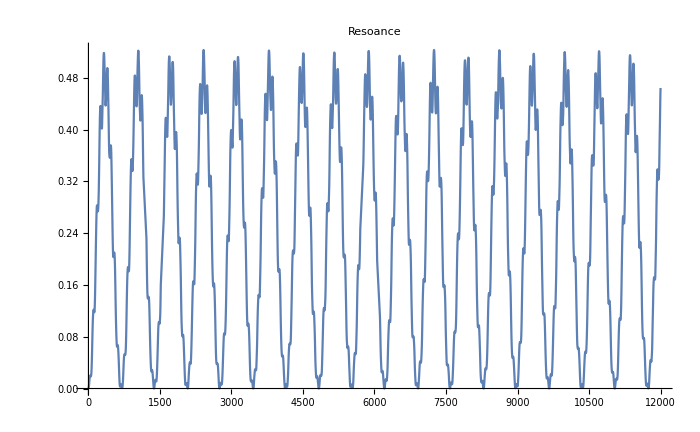

```mathematica
Plot[Evaluate[Abs[waveAM2[x]]^2/(Abs[waveAM1[x]]^2+Abs[waveAM2[x]]^2)/.solAM[[1]]],{x,0,endpoint},PlotLabel->"Resoance",ImageSize->imgsize]
```

### Scanning Parameters

```mathematica
testrangestart = 0;
testrangeend=endpoint;
ClearAll[resoScan]
resoScan[alpha0_,alpha1_,hamil_]:=Module[{},
Print["The resonance for constant + sin matter perturbation is at βr=",βr];
Manipulate[pltProb[NDSolve[{I D[{wave1[x],wave2[x]},x]==hamilAM[alpha0,alpha1,beta,x,hamil].{wave1[x],wave2[x]},{wave1[0],wave2[0]}==initAM},{wave1[x],wave2[x]},{x,testrangestart,testrangeend}],wave2,wave1,testrangestart,testrangeend,"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[beta],{"ω x","Probability"}],{{beta,βr,"Matter Frequency"},0.4,If[short,1.2,2.0],0.001},{{short,False,"Short Range"},{False,True}}]
]
```

```mathematica
0.951649/1.1
```

0.865135

```mathematica
resoScan[α0,α1,hamilVacSquare]
```

The resonance for constant + sin matter perturbation is at βr=0.951649

### Summary

```mathematica
ClearAll[plotRes]
```

```mathematica
plotRes[beta_,hamilVacBasis_,caption_:""]:=Module[{},
Print[ToString[caption]];
Print["Value of β is ",beta];
Print["Value of βr is ", βr]
Plot[Evaluate[Abs[wave2[x]]^2/(Abs[wave1[x]]^2+Abs[wave2[x]]^2)/.NDSolve[{I D[{wave1[x],wave2[x]},x]==hamilAM[α0,α1,beta,x,hamilVacBasis].{wave1[x],wave2[x]},{wave1[0],wave2[0]}==initAM},{wave1[x],wave2[x]},{x,0,endpoint}][[1]]],{x,0,endpoint},PlotLabel->"Resoance",ImageSize->imgsize,Frame->True]
]
```

Keep only Sigma1 term from matter contribution

Value of β is 1.008

Value of βr is 0.951649

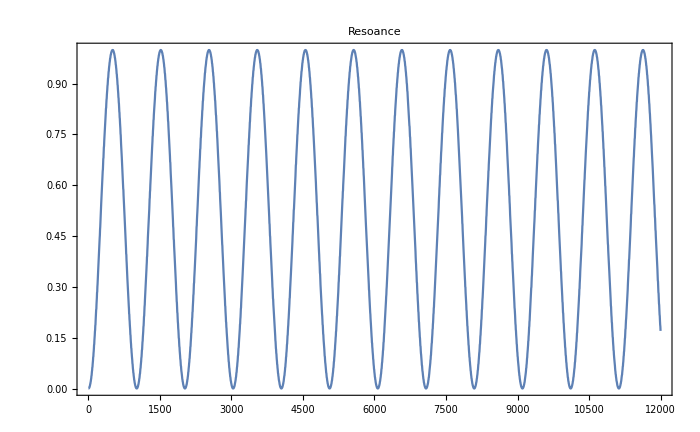
Null -Graphics-

```mathematica
plotRes[1.008,hamilVac1,"Keep only Sigma1 term from matter contribution"]
```

Keep only Sigma1 term from matter contribution

Value of β is 1.00765

Value of βr is 0.951649

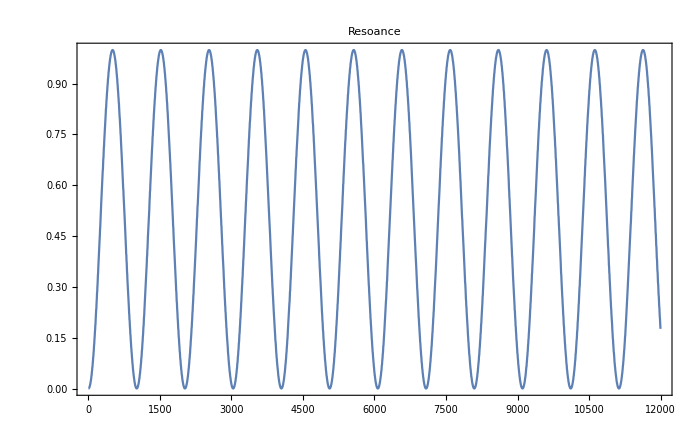
Null -Graphics-

```mathematica
plotRes[1.00765,hamilVac1,"Keep only Sigma1 term from matter contribution"]
```

Matter profile with 2 frequencies lambda =

Two frequencies in matter profile: sin(beta*x) and sin(2*beta*x)

Value of β is 0.475825

Value of βr is 0.951649

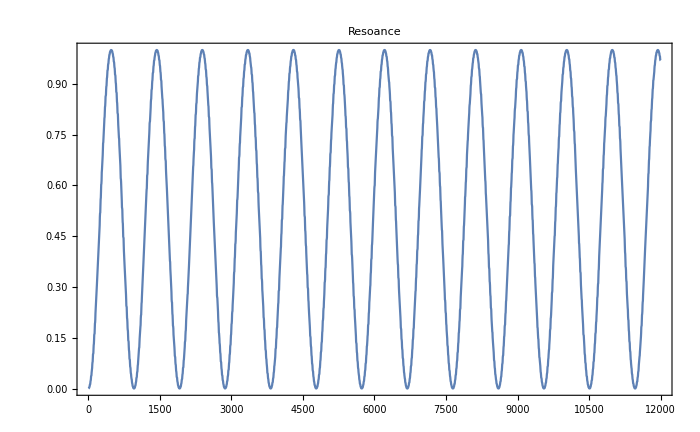
Null -Graphics-

```mathematica
plotRes[0.475825,hamilVac2Freq,"Two frequencies in matter profile: sin(beta*x) and sin(2*beta*x)"]
```

Two frequencies in matter profile: sin(beta*x) and sin(2*beta*x)

Value of β is 0.951649

Value of βr is 0.951649

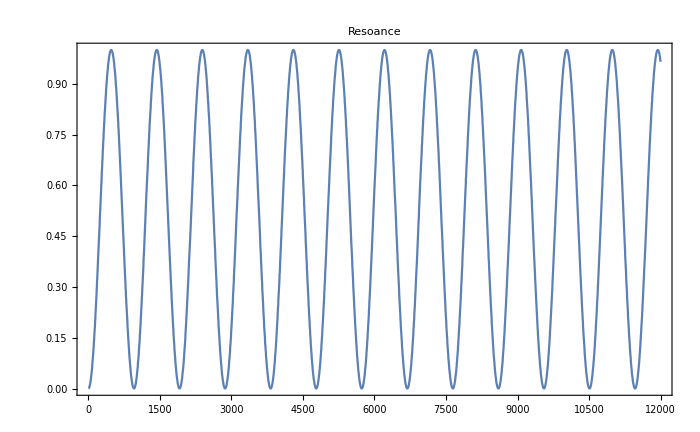
Null -Graphics-

```mathematica
plotRes[0.9516490253030304,hamilVac2Freq,"Two frequencies in matter profile: sin(beta*x) and sin(2*beta*x)"]
```

Two frequencies in matter profile: sin(beta*x) and sin(1.1*beta*x)

Value of β is 0.865135

Value of βr is 0.951649

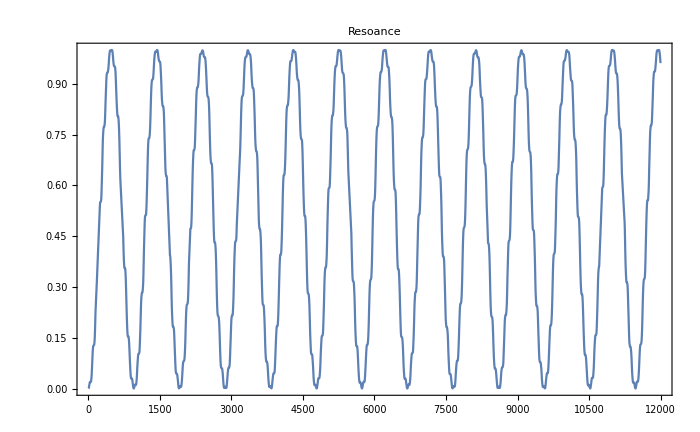
Null -Graphics-

```mathematica
plotRes[0.8651354545454545,hamilVac2FreqClose,"Two frequencies in matter profile: sin(beta*x) and sin(1.1*beta*x)"]
```

Two frequencies in matter profile: sin(beta*x) and sin(1.1*beta*x)

Value of β is 0.951649

Value of βr is 0.951649

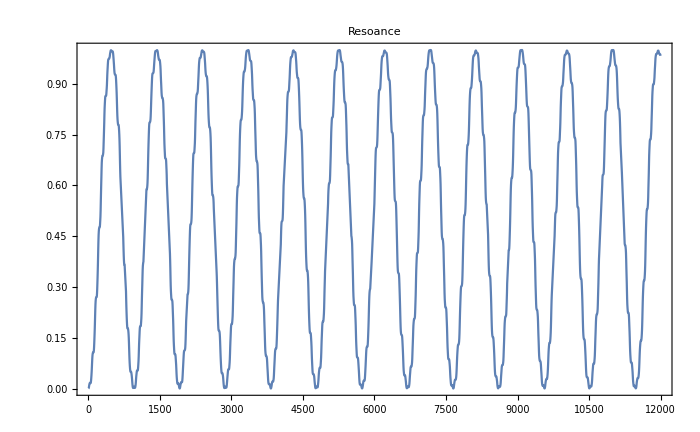
Null -Graphics-

```mathematica
plotRes[0.9516490253030304,hamilVac2FreqClose,"Two frequencies in matter profile: sin(beta*x) and sin(1.1*beta*x)"]
```

Square well: α0+α1*UnitStep@sin(beta*x)

Value of β is 0.949649

Value of βr is 0.951649

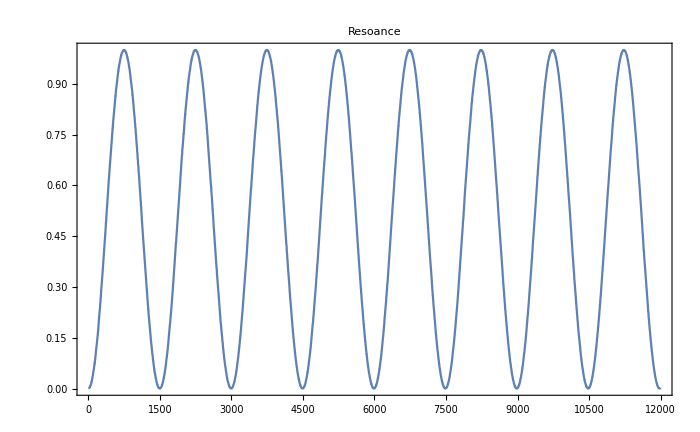
Null -Graphics-

```mathematica
plotRes[0.949649,hamilVacSquare,"Square well: α0+α1*UnitStep@sin(beta*x)"]
```

### Fourier Analyss

```mathematica
testFun[x_]:=Evaluate[Abs[waveAM2[x]]^2/(Abs[waveAM1[x]]^2+Abs[waveAM2[x]]^2)/.solAM[[1]]]
```

```mathematica
testFun[4]
```

0.000526228

```mathematica
testData=Table[testFun[x],{x,0,12000}]
```

{0.,0.0000298621,0.000263547,0.000480681,0.000526228,0.00104927,0.00177048,11987,0.442721,0.446368,0.453043,0.454968,0.456269,0.461423,0.464427}
 |  |  |  |

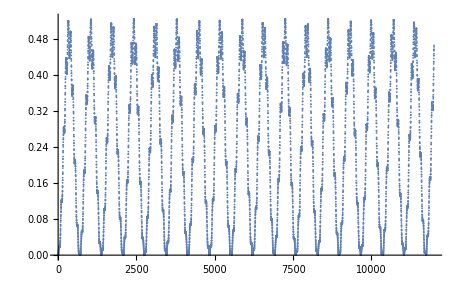

```mathematica
ListPlot[testData]
```

```mathematica
Manipulate[ListLinePlot[Abs[Fourier[testData]],PlotRange->{{start,end},All},ImageSize->imgsize],{{start,3,"Beginning"},0,endpoint},{{end,11900,"End"},0,endpoint}]
```

### Check the results

```mathematica
pltNorm[solAM,waveAM1,waveAM2,0,endpoint]
```

Dot::rect: Nonrectangular tensor encountered.

NDSolve::underdet: There are more dependent variables, {waveAM11[x], waveAM12[x], waveAM2[x]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {{ⅈ SuperscriptBox[{{waveAM11[0], « 1 »}, « 1 »} == {1, 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Dot::rect: Nonrectangular tensor encountered.

ReplaceAll::reps: {{ⅈ SuperscriptBox[{{waveAM11[0], waveAM12[0]}, waveAM2[0]} == {1, 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{(0.`  + 1.` ⅈ) SuperscriptBox[« 1 » == {1.`, 0.`} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot :: rect will be suppressed during this calculation.

-Graphics-

```mathematica
pltProb112=pltProb[solAM,waveAM2,waveAM1,0,endpoint,"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],{"ω x","Probability"}]
```

Dot::rect: Nonrectangular tensor encountered.

NDSolve::underdet: There are more dependent variables, {waveAM11[x], waveAM12[x], waveAM2[x]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {{ⅈ SuperscriptBox[{{waveAM11[0], « 1 »}, « 1 »} == {1, 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Dot::rect: Nonrectangular tensor encountered.

ReplaceAll::reps: {{ⅈ SuperscriptBox[{{waveAM11[0], waveAM12[0]}, waveAM2[0]} == {1, 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{(0.`  + 1.` ⅈ) SuperscriptBox[« 1 » == {1.`, 0.`} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot :: rect will be suppressed during this calculation.

-Graphics-

```mathematica
instHeavy2Re=Plot[Im[waveAM[x][[2]]]/.solAM,{x,0,50},PlotRange->All,PlotLabel->"Real Part of Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω="<>ToString[α1]<>"*λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_(λ, 2)|^2"},ImagePadding->imgpadding]
```

Dot::rect: Nonrectangular tensor encountered.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{{{ⅈ SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »], ⅈ SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]}, ⅈ SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Dot::rect: Nonrectangular tensor encountered.

NDSolve::dsvar: 1.02143 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{{{ⅈ SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »], ⅈ SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]}, ⅈ SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot :: rect will be suppressed during this calculation.

-Graphics-

## Stimulated?

```mathematica
adiabProb[thetavA_,alpha0A_,alpha1A_,betaA_,xA_]:=((Sin[thetavA]^2)( Sin[xA/2]^2))/((alpha0A+alpha1A*Sin[betaA*xA])^2+1-2(alpha0A+alpha1A*Sin[betaA*xA])Cos[2thetavA])
```

```mathematica
adiabDeno[thetavA_,omegavA_,alpha0A_,alpha1A_,betaA_,xA_]:=(alpha0A+alpha1A*Sin[betaA*xA])^2+1-2(alpha0A+alpha1A*Sin[betaA*xA])Cos[2thetavA]
```

```mathematica
vacOscProb[thetavA_,omegavA_,xA_]:=(Sin[thetavA]^2)( Sin[xA/2]^2)
```

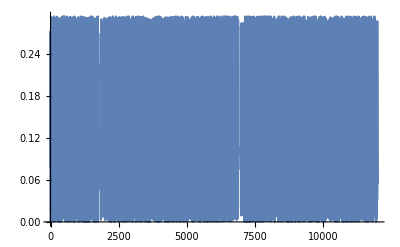

```mathematica
Plot[vacOscProb[θv,omegav,x],{x,0,endpoint}]
```

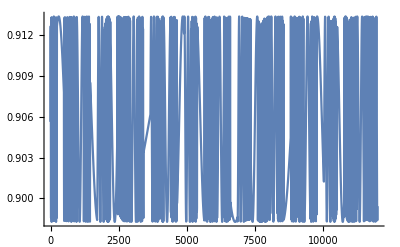

```mathematica
Plot[adiabDeno[θv,omegav,α0,α1,β,x],{x,0,endpoint}]
```

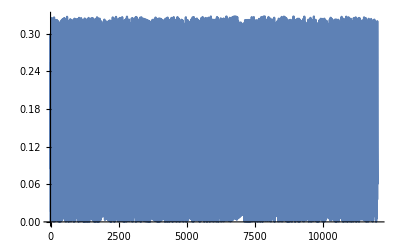

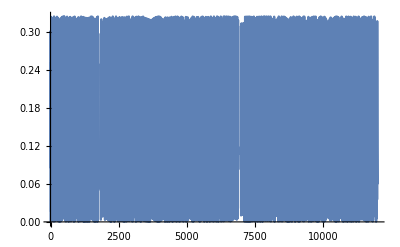

```mathematica
Plot[adiabProb[θv,α0,α1,β,x],{x,0,endpoint}]
Plot[adiabProb[θv,α0,0,β,x],{x,0,endpoint}]
```

## Temp

```mathematica
{{Cos[tv],-Sin[tv]},{Sin[tv],Cos[tv]}}.{{Cos[tm],Sin[tm]},{-Sin[tm],Cos[tm]}}//FullSimplify//MatrixForm
```

(Cos[tm-tv] | Sin[tm-tv]
-Sin[tm-tv] | Cos[tm-tv])